```mathematica
series=Import["/Users/peterkink/hopkins/COVID-19/csse_covid_19_data/csse_covid_19_time_series/time_series_covid19_confirmed_global.csv"];
transeries=Transpose[series];
transeries=Drop[transeries,1];
Dimensions[transeries]
hopdates=Drop[series[[1]],4]
%//Length
countriescsv=transeries[[1]];
%//Dimensions
hopdatetodate[dstring_]:=ToExpression["{"<>StringReplace[dstring,"/"->","]<>"}"][[{3,1,2}]]+{2000,0,0}
```

{102,265}

{1/22/20,1/23/20,1/24/20,1/25/20,1/26/20,1/27/20,1/28/20,1/29/20,1/30/20,1/31/20,2/1/20,2/2/20,2/3/20,2/4/20,2/5/20,2/6/20,2/7/20,2/8/20,2/9/20,2/10/20,2/11/20,2/12/20,2/13/20,2/14/20,2/15/20,2/16/20,2/17/20,2/18/20,2/19/20,2/20/20,2/21/20,2/22/20,2/23/20,2/24/20,2/25/20,2/26/20,2/27/20,2/28/20,2/29/20,3/1/20,3/2/20,3/3/20,3/4/20,3/5/20,3/6/20,3/7/20,3/8/20,3/9/20,3/10/20,3/11/20,3/12/20,3/13/20,3/14/20,3/15/20,3/16/20,3/17/20,3/18/20,3/19/20,3/20/20,3/21/20,3/22/20,3/23/20,3/24/20,3/25/20,3/26/20,3/27/20,3/28/20,3/29/20,3/30/20,3/31/20,4/1/20,4/2/20,4/3/20,4/4/20,4/5/20,4/6/20,4/7/20,4/8/20,4/9/20,4/10/20,4/11/20,4/12/20,4/13/20,4/14/20,4/15/20,4/16/20,4/17/20,4/18/20,4/19/20,4/20/20,4/21/20,4/22/20,4/23/20,4/24/20,4/25/20,4/26/20,4/27/20,4/28/20,4/29/20}

99

{265}

```mathematica
TableForm[transeries];
```

```mathematica
CountryData["Japan","Population"]
```

126225259

```mathematica
{"Singapore",200,{2.835279843883035*^8,64.38918662693713,0.1259411788554341},21,7,10,0},
```

```mathematica
{"Spain",300,{215675.98160202175,3181.500137016704,0.14826151757050574},28,14,10,0},
```

```mathematica
countryparameters=
(*name,truncdrop,jp0,lag,projtime,bootlag,plotdrop*)
{
{"Canada",200,{52180.39484847384,1005.9304582251706,0.1324225337960489},21,21,10,0},{"Australia",100,{6540.8364412808105,85.77223261633138,0.2345420078562459},21,21,10,0},{"New Zealand",5,{1441.2482649030032,14.971640930135235,0.23959274221723975},21,21,10,0},{"Croatia",10,{1985.7723787465545,21.596481176857367,0.1589401951808019},21,21,10,5},{"Czechia",10,{7096.988271837173,68.14371590582019,0.16461693785708748},21,21,10,5},
{"Sweden",200,{23138.83457722449,461.922977379802,0.10293773671900139},28,14,10,0},
{"Greece",50,{2469.7252428688025,97.9216579531985,0.1381653045706424},28,21,10,0},
{"Japan",950,{17986.663577976567,576.9474735585374,0.12382285884487645},28,14,8,0},
{"Denmark",1100,{9249.181828199724,848.3550476707888,0.11809736637519559},28,14,10,0},
{"Russia",300,{133764.28972174952,345.7178233894532,0.17211220984196077},21,14,10,0},
{"United Kingdom",200,{181106.79697173668,1069.9501757425367,0.1337539999625829},21,14,10,0}
}
```

{{Canada,200,{52180.4,1005.93,0.132423},21,21,10,0},{Australia,100,{6540.84,85.7722,0.234542},21,21,10,0},{New Zealand,5,{1441.25,14.9716,0.239593},21,21,10,0},{Croatia,10,{1985.77,21.5965,0.15894},21,21,10,5},{Czechia,10,{7096.99,68.1437,0.164617},21,21,10,5},{Sweden,200,{23138.8,461.923,0.102938},28,14,10,0},{Greece,50,{2469.73,97.9217,0.138165},28,21,10,0},{Japan,950,{17986.7,576.947,0.123823},28,14,8,0},{Denmark,1100,{9249.18,848.355,0.118097},28,14,10,0},{Russia,300,{133764.,345.718,0.172112},21,14,10,0},{United Kingdom,200,{181107.,1069.95,0.133754},21,14,10,0}}

```mathematica
countryparameters
```

{{Canada,200,{59480.2,1199.5,0.121519},21,21,10,0},{Australia,100,{6584.94,90.3971,0.230911},21,21,10,0},{New Zealand,5,{1451.79,15.7679,0.236071},21,21,10,0},{Croatia,10,{2039.34,24.3694,0.152989},21,21,10,5},{Czechia,10,{7313.84,79.9922,0.156961},21,21,10,5},{Sweden,200,{24104.7,484.678,0.100472},28,14,10,0},{Greece,50,{2501.64,102.119,0.13532},28,21,10,0},{Japan,950,{17796.2,513.868,0.123981},28,14,8,0},{Denmark,1100,{9443.74,871.643,0.115132},28,14,10,0},{Russia,300,{137784.,359.95,0.170215},21,14,10,0}}

```mathematica
Export["/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/countryparameters.xml",countryparameters]
```

/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/countryparameters.xml

```mathematica
countryparameters=Import["/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/countryparameters.xml"]
```

{{Spain,300,{215676.,3181.5,0.148262},28,14,10,0},{Canada,200,{54700.6,1073.56,0.12833},21,21,10,0},{Australia,100,{6563.71,88.1183,0.232672},21,21,10,0},{New Zealand,5,{1447.14,15.4045,0.237648},21,21,10,0},{Croatia,10,{2017.72,23.1855,0.15542},21,21,10,5},{Czechia,10,{7216.09,74.357,0.160426},21,21,10,5},{Sweden,200,{23138.8,461.923,0.102938},28,14,10,0},{Greece,50,{2469.73,97.9217,0.138165},28,21,10,0},{Japan,950,{17951.8,517.917,0.123382},28,14,8,0}}

```mathematica
"Spain",
```

```mathematica
wolfcountrynames={"Canada","Australia","New Zealand","Croatia","CzechRepublic","Sweden","Greece","Japan","Denmark","Russia","United Kingdom"};
wpopulations=Map[CountryData[#,"Population"][[1]]&,wolfcountrynames]
```

{35309555,23502754,4554858,4369961,10611300,9595619,11470255,126225259,5628958,142400066,63556184}

```mathematica
countrybootabcs={};
```

```mathematica
SetDirectory["/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/plotdump"]
```

/Users/peterkink/githubclone/pandemic-of-2020/docs/countries/plotdump

country : Canada

data length : 46

start date : {2020,3,15}

jdp0 : {62373.,1283.07,0.117602}

jp20 : {79769.8,2663.96,0.0879467}

backward result : {19758.,271.885,0.236761}

forward result : {79769.8,2663.96,0.0879467}

last tab: {79769.8,2663.96,0.0879467}

backward result : {19758.,271.885,0.236761}

forward result : {79769.8,2663.96,0.0879467}

past errors : {{1168.42,1671.19,2760.45,3296.45,3889.18,4386.5,5165.31,5934.66,6721.99,7754.2},4274.83}

boot tab : {{45964.5,1055.02,0.134761},{40413.3,945.381,0.143646},{47860.2,1228.25,0.127227},{57820.1,1589.,0.11208},{69248.4,1966.04,0.100292},{78777.9,2323.85,0.0919712},{96797.7,2733.85,0.0835396},{120684.,3157.66,0.0764033},{182039.,3637.78,0.0690106},{230772.,3965.05,0.0651527},{261492.,4221.32,0.0627344},{299529.,4547.98,0.0600505},{209723.,4506.01,0.0616834},{159262.,4447.61,0.0636705},{127431.,4244.93,0.0669304},{112896.,4043.81,0.0697297}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46}

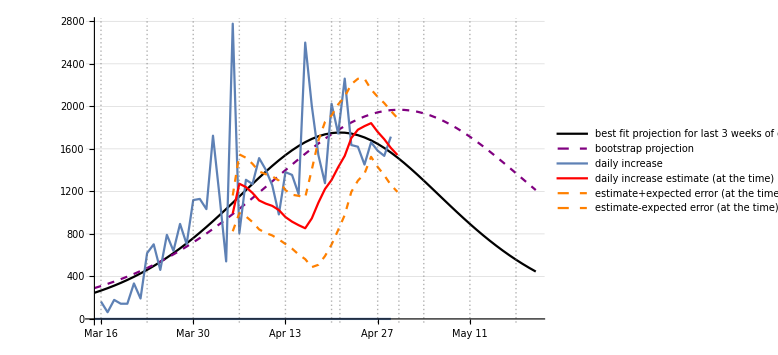

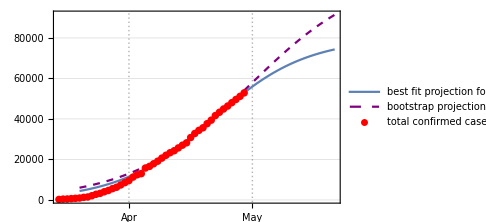

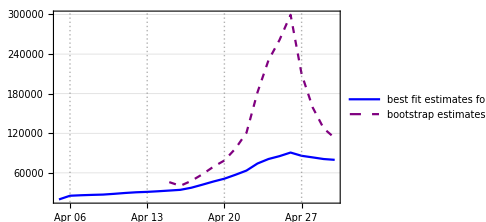

April 29

Canadadate.txt

Canadagraf.png

Canadaloggraf.png

Canadadfgraf.png

Canadafinalplot.png

country : Australia

data length : 51

start date : {2020,3,10}

jdp0 : {6604.92,92.6316,0.229235}

jp20 : {6827.77,1458.86,0.112301}

backward result : {6333.48,61.3826,0.258068}

forward result : {6827.77,1458.86,0.112301}

last tab: {6827.77,1458.86,0.112301}

backward result : {6333.48,61.3826,0.258068}

forward result : {6827.77,1458.86,0.112301}

past errors : {{56.3591,66.4786,63.5721,65.3163,73.4392,84.7129,99.9463,102.98,122.679,127.934},86.3418}

boot tab : {{6236.05,65.0561,0.254921},{6538.97,99.7277,0.227185},{6680.96,127.765,0.212343},{6659.47,126.959,0.213015},{6685.33,145.069,0.206255},{6716.95,169.703,0.198415},{6739.39,206.803,0.189174},{6767.52,252.699,0.179859},{6868.31,385.44,0.159561},{6930.96,513.821,0.14614},{6988.52,689.771,0.132765},{6950.09,730.47,0.131633},{6956.65,930.089,0.122078},{7011.34,1279.75,0.10784},{7030.75,1582.12,0.0988361},{7051.54,1928.15,0.0901406},{7033.47,2055.46,0.0881846},{7051.65,2328.51,0.0823429},{6996.74,2315.34,0.0848807},{7041.47,2891.12,0.0734227},{7032.95,3194.97,0.0691873}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51}

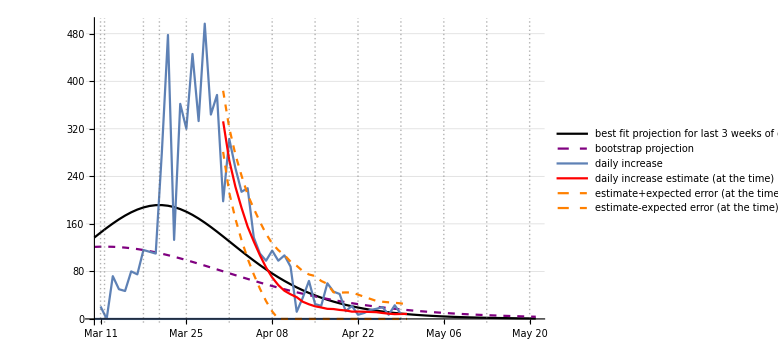

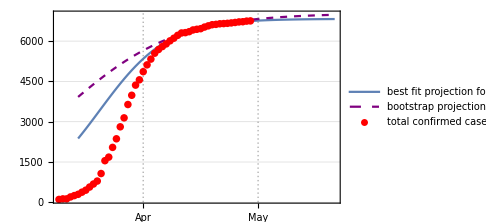

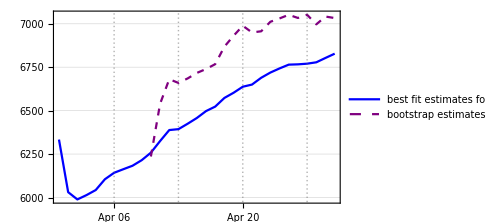

April 29

Australiadate.txt

Australiagraf.png

Australialoggraf.png

Australiadfgraf.png

Australiafinalplot.png

country : New Zealand

data length : 47

start date : {2020,3,14}

jdp0 : {1455.66,16.087,0.234724}

jp20 : {1487.16,94.8217,0.160519}

backward result : {981.19,4.49853,0.341492}

forward result : {1487.16,94.8217,0.160519}

last tab: {1487.16,94.8217,0.160519}

backward result : {981.19,4.49853,0.341492}

forward result : {1487.16,94.8217,0.160519}

past errors : {{10.3349,11.2799,14.0202,16.4025,19.302,26.6176,24.2677,26.1862,27.3201,28.6266},20.4358}

boot tab : {{1833.01,53.1616,0.158085},{1745.34,52.5281,0.161741},{1653.58,49.0838,0.169019},{1584.85,44.396,0.177548},{1536.2,38.8581,0.18697},{1509.47,34.2446,0.194769},{1500.49,32.6958,0.197606},{1488.29,29.0462,0.2039},{1478.53,26.5983,0.208752},{1482.16,31.3381,0.201653},{1481.68,34.8448,0.197617},{1486.04,47.1765,0.185404},{1494.82,73.9462,0.167186},{1492.82,86.0635,0.162189},{1499.51,118.295,0.149442},{1507.24,167.934,0.135325},{1512.91,217.538,0.124841}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47}

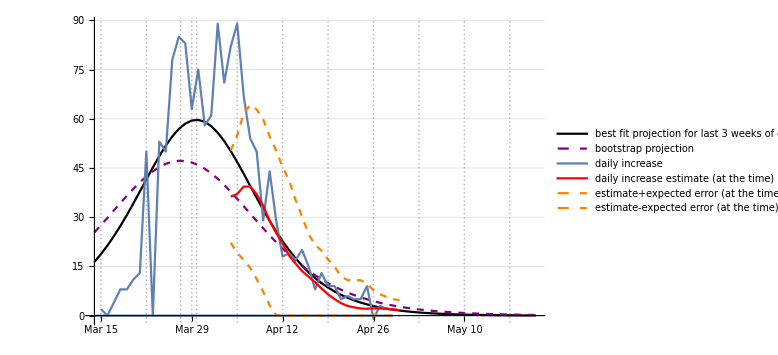

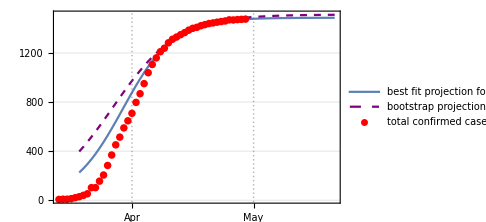

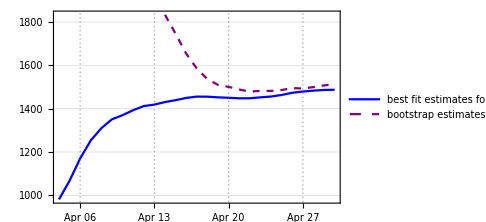

April 29

newzealanddate.txt

newzealandgraf.png

newzealandloggraf.png

newzealanddfgraf.png

newzealandfinalplot.png

country : Croatia

data length : 55

start date : {2020,3,6}

jdp0 : {2055.12,25.3125,0.151161}

jp20 : {2142.67,49.1174,0.126816}

backward result : {835.937,1.62704,0.316962}

forward result : {2142.67,49.1174,0.126816}

last tab: {2142.67,49.1174,0.126816}

backward result : {835.937,1.62704,0.316962}

forward result : {2142.67,49.1174,0.126816}

past errors : {{-34.7681,-36.9091,-21.711,-15.2951,-9.789,-23.3237,-28.031,-36.0413,-43.4821,-42.4764},-29.1827}

boot tab : {{1753.63,15.3017,0.178544},{1699.93,15.2697,0.179765},{1759.03,17.9074,0.171919},{1918.37,24.168,0.156701},{2031.8,30.4091,0.145864},{2234.16,41.1379,0.131574},{2212.36,46.4471,0.12736},{2419.65,61.3622,0.114706},{2598.91,77.5604,0.104611},{2869.15,98.1151,0.0943032},{3065.29,117.977,0.0868374},{3424.2,144.853,0.0782348},{3431.63,159.817,0.0751471},{3255.65,166.798,0.0748764},{3196.99,179.479,0.0731036},{2820.71,167.394,0.0783883},{2641.69,157.695,0.0823438},{2493.49,137.335,0.0886636},{2381.1,117.462,0.0953606},{2286.,92.5786,0.104378},{2191.95,63.4271,0.117748},{2120.17,38.0182,0.134455},{2098.87,30.1953,0.141603},{2101.61,30.1679,0.141487},{2105.82,31.8647,0.139904}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55}

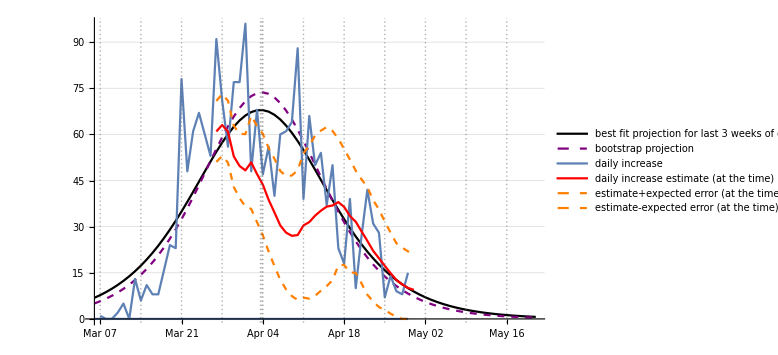

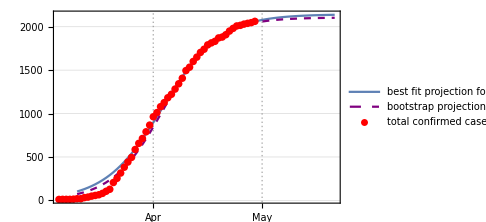

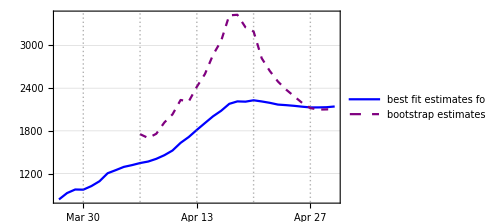

April 29

Croatiadate.txt

Croatiagraf.png

Croatialoggraf.png

Croatiadfgraf.png

Croatiafinalplot.png

country : Czechia

data length : 56

start date : {2020,3,5}

jdp0 : {7400.94,85.4997,0.153839}

jp20 : {8767.16,1164.58,0.0672592}

backward result : {2216.85,9.55805,0.303903}

forward result : {8767.16,1164.58,0.0672592}

last tab: {8767.16,1164.58,0.0672592}

backward result : {2216.85,9.55805,0.303903}

forward result : {8767.16,1164.58,0.0672592}

past errors : {{194.703,279.193,336.02,354.423,408.716,460.283,488.576,509.111,550.46,610.248},419.173}

boot tab : {{9746.37,89.0792,0.147415},{8757.52,93.6428,0.147021},{7322.81,77.909,0.158933},{6079.92,47.0909,0.186442},{6848.02,73.7599,0.16362},{7931.86,112.511,0.142321},{8162.42,128.142,0.136611},{8321.56,143.242,0.131976},{8165.76,146.739,0.131839},{7956.08,149.669,0.132238},{7426.67,128.353,0.140741},{7457.47,143.195,0.137005},{7719.14,184.128,0.127089},{7803.91,208.119,0.122653},{7528.09,173.829,0.130412},{7492.7,175.735,0.130394},{7657.59,229.587,0.120863},{7980.6,340.932,0.106464},{8354.69,521.848,0.0914293},{8663.22,700.572,0.0810726},{9307.2,1016.19,0.0671598},{9728.51,1209.91,0.0604686},{10030.2,1438.86,0.0545394},{10339.,1677.93,0.0492557},{11487.9,2098.19,0.0400292},{12086.1,2318.22,0.0361193}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56}

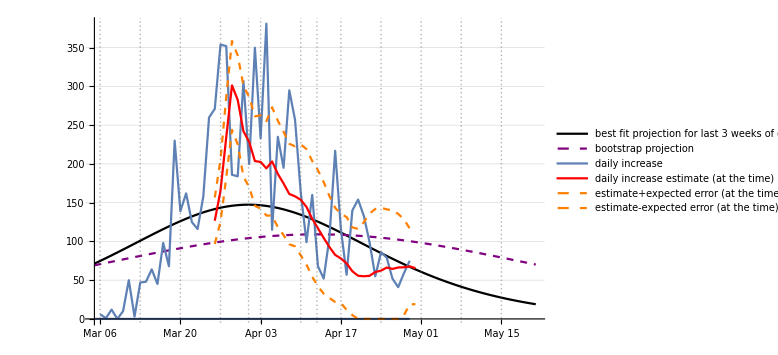

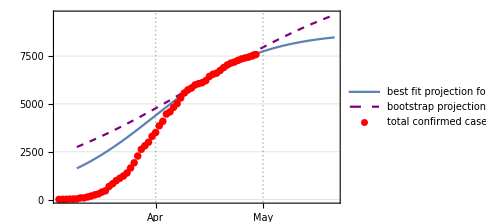

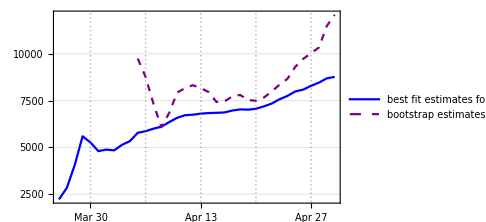

April 29

Czechiadate.txt

Czechiagraf.png

Czechialoggraf.png

Czechiadfgraf.png

Czechiafinalplot.png

country : Sweden

data length : 53

start date : {2020,3,8}

jdp0 : {25128.7,510.707,0.0978952}

jp20 : {30173.3,876.605,0.07949}

backward result : {33816.,391.165,0.107741}

forward result : {30173.3,876.605,0.07949}

last tab: {30173.3,876.605,0.07949}

backward result : {33816.,391.165,0.107741}

forward result : {30173.3,876.605,0.07949}

past errors : {{224.021,364.207,665.594,1060.33,1540.26,1841.94,2019.72,2042.73,2496.01,2955.46},1521.03}

boot tab : {{14328.6,230.525,0.14094},{15189.8,252.891,0.1354},{16812.4,298.978,0.126058},{18482.6,343.08,0.118537},{18921.5,352.548,0.116978},{18681.,340.621,0.118503},{18698.9,343.557,0.118173},{19793.6,391.331,0.112252},{22360.6,500.522,0.101305},{25768.5,630.977,0.0912165},{30601.6,789.143,0.081737},{35234.9,926.372,0.0752642},{38271.4,1035.56,0.071228},{37837.5,1089.33,0.0700247},{40186.1,1191.01,0.0670223},{42912.6,1301.13,0.0640638}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53}

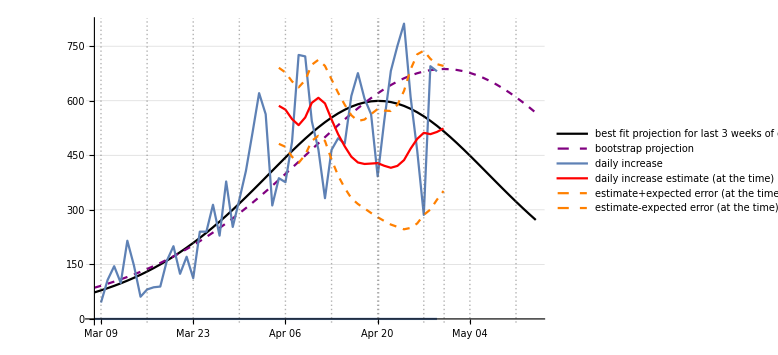

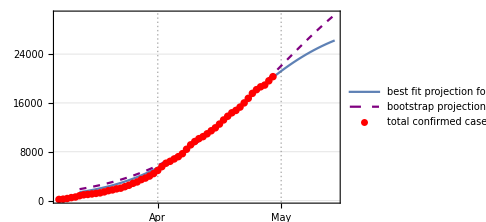

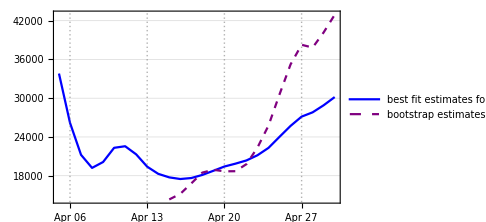

April 29

Swedendate.txt

Swedengraf.png

Swedenloggraf.png

Swedendfgraf.png

Swedenfinalplot.png

country : Greece

data length : 53

start date : {2020,3,8}

jdp0 : {2532.3,106.447,0.132556}

jp20 : {2813.36,404.97,0.0776928}

backward result : {2478.4,89.1455,0.143581}

forward result : {2813.36,404.97,0.0776928}

last tab: {2813.36,404.97,0.0776928}

backward result : {2478.4,89.1455,0.143581}

forward result : {2813.36,404.97,0.0776928}

past errors : {{-30.2514,113.648,110.113,155.955,175.001,184.102,189.121,200.941,228.458,234.58},156.167}

boot tab : {{2352.44,85.4084,0.14789},{2343.2,82.2574,0.149785},{2378.88,87.4267,0.14601},{2379.53,86.5441,0.146415},{2374.13,85.708,0.147053},{2332.45,75.2657,0.15395},{2313.2,68.0001,0.158783},{2460.69,105.336,0.135574},{2480.71,114.594,0.131611},{2574.66,155.517,0.116975},{2663.68,207.482,0.103821},{2751.31,268.599,0.0923139},{2831.38,333.203,0.0829139},{2981.54,446.152,0.0698082},{3254.89,597.533,0.0555793},{3545.4,723.148,0.0460135}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53}

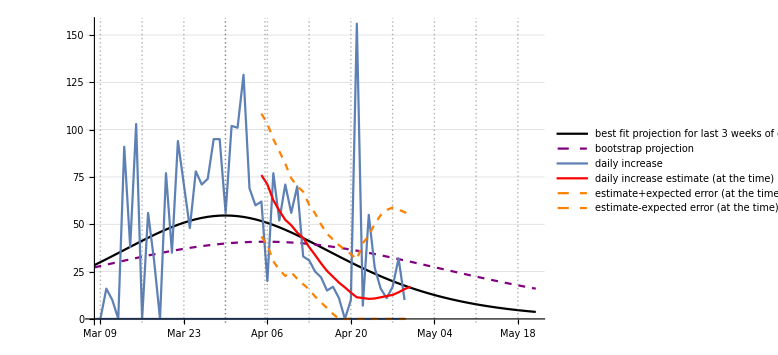

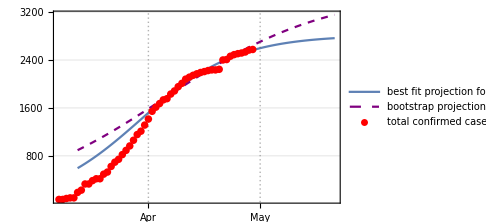

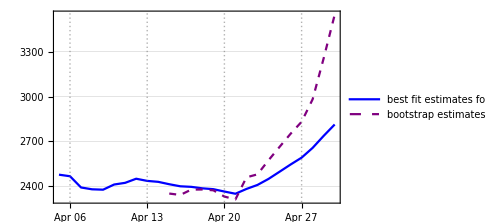

April 29

Greecedate.txt

Greecegraf.png

Greeceloggraf.png

Greecedfgraf.png

Greecefinalplot.png

country : Japan

data length : 41

start date : {2020,3,20}

jdp0 : {16815.7,474.946,0.129341}

jp20 : {15853.3,337.153,0.145241}

backward result : {61680.7,682.989,0.0970644}

forward result : {15853.3,337.153,0.145241}

last tab: {15853.3,337.153,0.145241}

backward result : {61680.7,682.989,0.0970644}

forward result : {15853.3,337.153,0.145241}

past errors : {{-612.933,-264.82,-288.365,-345.589,-568.092,-261.026,-1055.05,-1245.29},-580.146}

boot tab : {{13315.9,224.523,0.172372},{12884.9,183.951,0.183025},{12913.8,169.381,0.18627},{13895.7,210.611,0.172145},{14183.,221.253,0.168669},{14778.9,252.027,0.160776}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41}

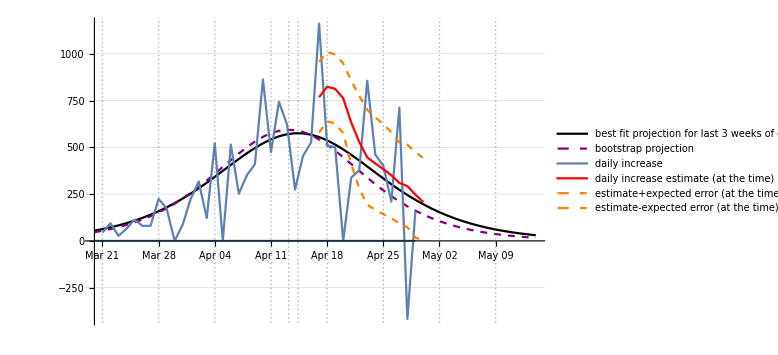

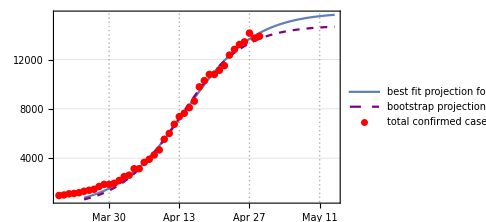

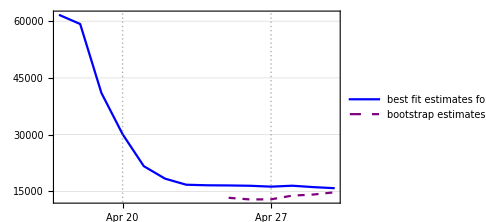

April 29

Japandate.txt

Japangraf.png

Japanloggraf.png

Japandfgraf.png

Japanfinalplot.png

country : Denmark

data length : 43

start date : {2020,3,18}

jdp0 : {9643.05,897.269,0.112091}

jp20 : {10066.4,1182.65,0.0970871}

backward result : {9622.11,847.804,0.116597}

forward result : {10066.4,1182.65,0.0970871}

last tab: {10066.4,1182.65,0.0970871}

backward result : {9622.11,847.804,0.116597}

forward result : {10066.4,1182.65,0.0970871}

past errors : {{56.304,135.931,263.062,345.828,411.377,582.893,656.6,729.773,838.739,956.879},497.738}

boot tab : {{8789.2,690.271,0.132732},{9408.77,861.385,0.115934},{9904.5,1019.76,0.104163},{10433.3,1208.42,0.0930967},{11116.9,1440.04,0.0818724},{12051.9,1723.91,0.0705372}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43}

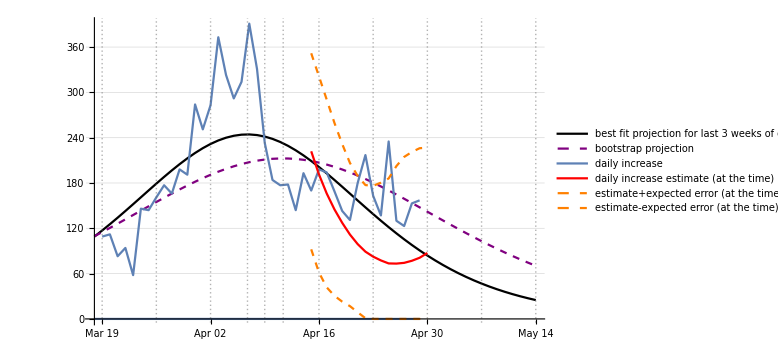

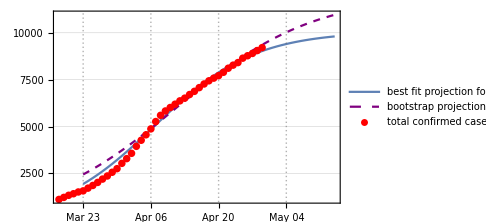

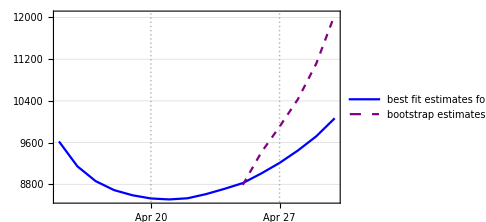

April 29

Denmarkdate.txt

Denmarkgraf.png

Denmarkloggraf.png

Denmarkdfgraf.png

Denmarkfinalplot.png

country : Russia

data length : 40

start date : {2020,3,21}

jdp0 : {145993.,393.321,0.166189}

jp20 : {146648.,399.664,0.165592}

backward result : {40899.,291.658,0.19182}

forward result : {146648.,399.664,0.165592}

last tab: {146648.,399.664,0.165592}

backward result : {40899.,291.658,0.19182}

forward result : {146648.,399.664,0.165592}

past errors : {{-1450.48,-2570.74,-4826.37,-8293.42,-11439.4,-15208.3,-19286.2,-24172.2,-29407.7,-35670.2},-15232.5}

boot tab : {{339753.,540.719,0.148964},{272232.,541.224,0.149824},{216291.,537.8,0.151313},{166931.,488.092,0.156903},{148516.,426.755,0.163075},{133704.,340.318,0.172608},{134487.,325.5,0.174075},{134147.,304.939,0.176344},{130117.,251.508,0.183418},{113530.,111.805,0.213888}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40}

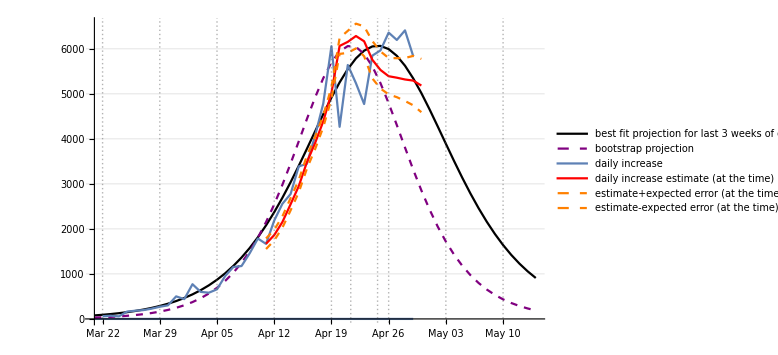

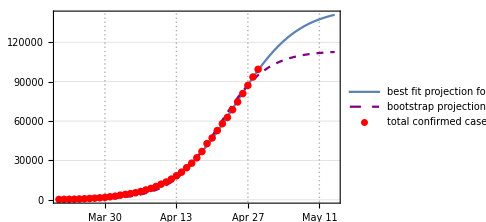

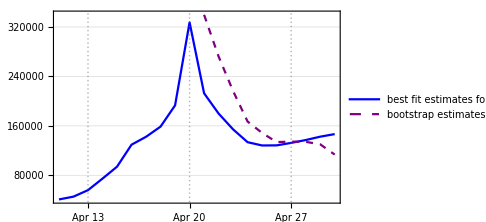

April 29

Russiadate.txt

Russiagraf.png

Russialoggraf.png

Russiadfgraf.png

Russiafinalplot.png

country : United Kingdom

data length : 54

start date : {2020,3,7}

jdp0 : {181107.,1069.95,0.133754}

jp20 : {213573.,3488.85,0.0989553}

backward result : {109233.,204.099,0.209633}

forward result : {213573.,3488.85,0.0989553}

last tab: {213573.,3488.85,0.0989553}

backward result : {109233.,204.099,0.209633}

forward result : {213573.,3488.85,0.0989553}

past errors : {{2627.17,3325.94,4485.05,6088.29,8767.16,11255.,13538.1,15901.4,18173.5,20732.7},10489.4}

boot tab : {{83241.9,195.501,0.211712},{78715.9,169.211,0.218966},{104119.,386.441,0.179579},{124173.,562.919,0.162089},{161690.,722.568,0.149431},{167872.,807.496,0.145055},{167177.,860.08,0.143001},{161292.,887.738,0.142526},{173543.,1053.12,0.13579},{164724.,1037.13,0.137269},{173159.,1212.29,0.131495},{191688.,1498.9,0.123273},{201406.,1708.79,0.1186},{216532.,2016.16,0.112684},{204744.,2024.87,0.113565},{199855.,2112.68,0.112913},{199191.,2256.34,0.111236},{206738.,2631.07,0.106331},{218142.,3158.27,0.100419},{233208.,3921.28,0.0935452},{245292.,4596.52,0.0886055},{256027.,5373.87,0.0839984},{266253.,6354.42,0.0792965},{271707.,7244.,0.0758797}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54}

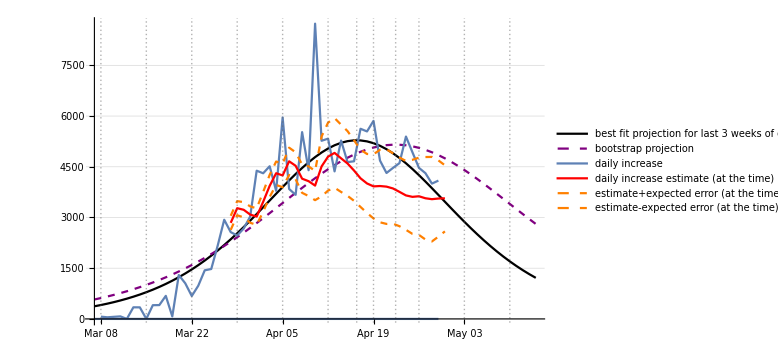

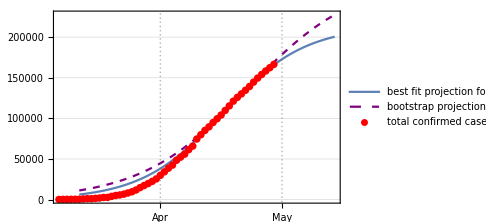

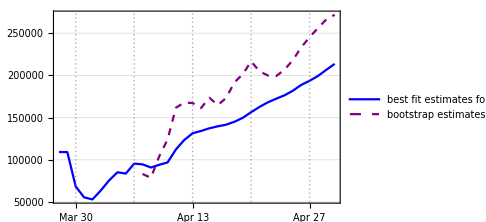

April 29

United Kingdomdate.txt

United Kingdomgraf.png

United Kingdomloggraf.png

United Kingdomdfgraf.png

United Kingdomfinalplot.png

{41.95657,Null}

```mathematica
countrydateplotlist={};
Timing[
For[cit=1,cit≤Length[countryparameters],cit++,
countrynames=Transpose[countryparameters][[1]];
currentnamme=countrynames[[cit]];
{currentnamme,ctrunc,jdp0,jlag,jprojtime,jbootlag,jplotdrop}=countryparameters[[cit]];
Print["country : ",currentnamme];
countinds=Flatten[Position[countriescsv,currentnamme]];
countrydata=Drop[Map[Total,Transpose[series[[countinds]]]],4];
datesanddata=Transpose[{Map[hopdatetodate,hopdates],countrydata}];

truncdatesandata=Select[datesanddata,#[[2]]>ctrunc&];
justdata=Transpose[truncdatesandata][[2]];
justtime=Table[i,{i,Length[justdata]}];
(*jstartdate=truncdatesandata[[1,1]]-{0,0,1}*)
jstartdate=truncdatesandata[[1,1]];
Print["data length : ",Length[justdata]];
Print["start date : ",jstartdate];

{jdp0,tp1,tp2,tp3}=GNiteration[justdata,jdp0,justtime];
Print["jdp0 : ",jdp0];
{jp20,jabctab,jwinds}=stepGNiteration[justdata,jdp0,jlag,justtime,{1,0}];
Print["jp20 : ",jp20];

(*update jdp0*)
countryparameters[[cit,3]]=jdp0;

{jgraf,jloggraf,jdfpplot,jprogplot,jfinal,jbootabc}=somegraphs[jdp0,jp20,justtime,justdata,jstartdate,jlag,jprojtime,5,jbootlag,wpopulations[[cit]]];
jdatestring=reldatetostring[jstartdate,justtime[[-1]]-1];
Print[jgraf];
Print[jloggraf];
Print[jfinal];

(*jdatestring=reldatetostring[cpstartdate,timecpert[[-1]]];*)

Print[jdatestring];

(*new zealand string exception*)
If[currentnamme==="New Zealand",currentnamme="newzealand"];
(*uk  string exception*)
If[currentnamme==="United Kingdom",currentnamme="uk"];

datefilename=currentnamme<>"date.txt";
Print[datefilename];
Export[datefilename,jdatestring];
graffilename=currentnamme<>"graf.png";
Export[graffilename,jgraf];
Print[graffilename];
loggraffilename=currentnamme<>"loggraf.png";
Export[loggraffilename,jloggraf];
Print[loggraffilename];
dfgraffilename=currentnamme<>"dfgraf.png";
Export[dfgraffilename,jdfpplot];
Print[dfgraffilename];
finalgraffilename=currentnamme<>"finalplot.png";
Export[finalgraffilename,jfinal];
Print[finalgraffilename];

drcases=Transpose[datesanddata][[2]];
drcases=drcases/wpopulations[[cit]];
datesanddata=Transpose[{Transpose[datesanddata][[1]],drcases}];
countrydateplotlist=AppendTo[countrydateplotlist,datesanddata];
]
]
```

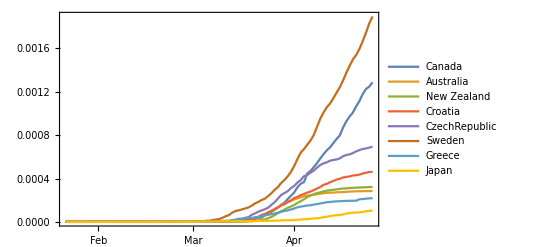

```mathematica
DateListPlot[countrydateplotlist,PlotLegends->wolfcountrynames,PlotRange->All]
```

```mathematica
allcountrynames=Join[fwcountrynames,wolfcountrynames]
%//Length
Length[countrybootabcs]
```

{Slovenia,Italy,Austria,Germany,USA,Canada,Australia,New Zealand,Croatia,CzechRepublic,Singapore,Japan}

12

12

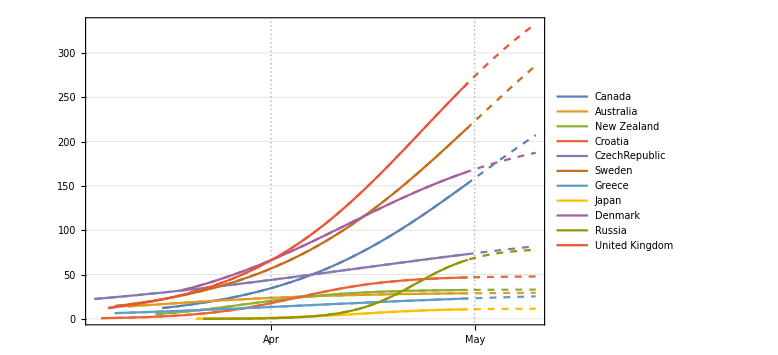

```mathematica
projfwcountryplot=DateListPlot[countrybootabcs,PlotRange->All,ImageSize->Large,PlotTheme->"Detailed",PlotStyle->Dashed];
trunccountrybootabcs=Map[Drop[#,-grafprojtime]&,countrybootabcs];
pastfwcountryplot=DateListPlot[trunccountrybootabcs,PlotRange->All,PlotLegends->wolfcountrynames,ImageSize->Large,PlotTheme->"Detailed"];
mscprojplots=Show[projfwcountryplot,pastfwcountryplot,ImageSize->Large]
```

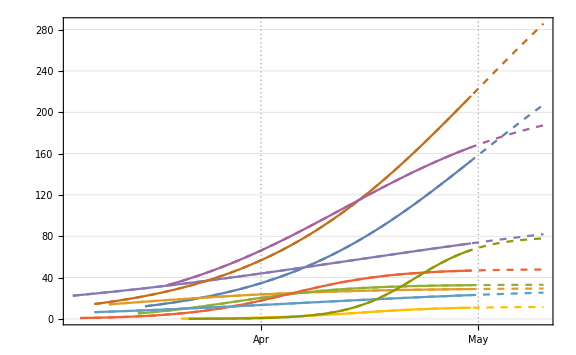
```mathematica
29.4.
-Graphics-
```

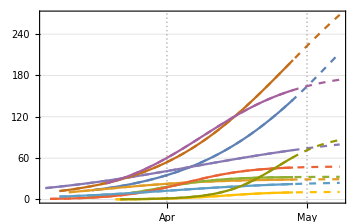
```mathematica
28.4.
-Graphics-
```

```mathematica
Export["mscprojplots.png",mscprojplots]
```

mscprojplots.png

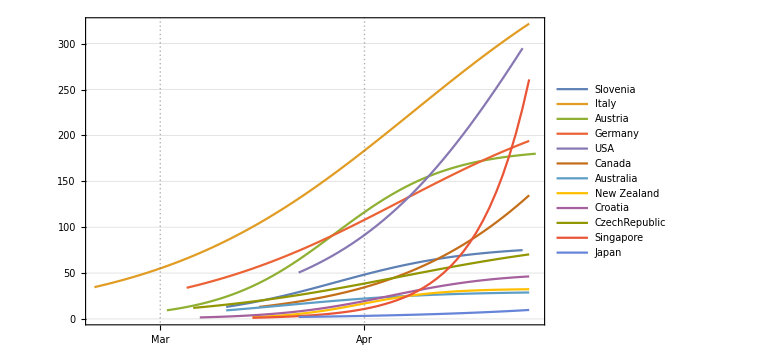

```mathematica
DateListPlot[countrybootabcs,PlotRange->All,PlotLegends->allcountrynames,ImageSize->Large,PlotTheme->"Detailed"]
```

```mathematica
ColorData
```

```mathematica
countinds=Flatten[Position[countriescsv,"United Kingdom"]]
countrydata=Drop[Map[Total,Transpose[series[[countinds]]]],4];
datesanddata=Transpose[{Map[hopdatetodate,hopdates],countrydata}]
```

{219,220,221,222,223,224,225,251,252,253,260}

{{{2020,1,22},0},{{2020,1,23},0},{{2020,1,24},0},{{2020,1,25},0},{{2020,1,26},0},{{2020,1,27},0},{{2020,1,28},0},{{2020,1,29},0},{{2020,1,30},0},{{2020,1,31},2},{{2020,2,1},2},{{2020,2,2},2},{{2020,2,3},2},{{2020,2,4},2},{{2020,2,5},2},{{2020,2,6},2},{{2020,2,7},3},{{2020,2,8},3},{{2020,2,9},3},{{2020,2,10},8},{{2020,2,11},8},{{2020,2,12},9},{{2020,2,13},9},{{2020,2,14},9},{{2020,2,15},9},{{2020,2,16},9},{{2020,2,17},9},{{2020,2,18},9},{{2020,2,19},9},{{2020,2,20},9},{{2020,2,21},9},{{2020,2,22},9},{{2020,2,23},9},{{2020,2,24},13},{{2020,2,25},13},{{2020,2,26},13},{{2020,2,27},15},{{2020,2,28},20},{{2020,2,29},23},{{2020,3,1},36},{{2020,3,2},40},{{2020,3,3},51},{{2020,3,4},86},{{2020,3,5},116},{{2020,3,6},164},{{2020,3,7},207},{{2020,3,8},274},{{2020,3,9},322},{{2020,3,10},384},{{2020,3,11},459},{{2020,3,12},459},{{2020,3,13},802},{{2020,3,14},1144},{{2020,3,15},1145},{{2020,3,16},1551},{{2020,3,17},1960},{{2020,3,18},2642},{{2020,3,19},2716},{{2020,3,20},4014},{{2020,3,21},5067},{{2020,3,22},5745},{{2020,3,23},6726},{{2020,3,24},8164},{{2020,3,25},9640},{{2020,3,26},11812},{{2020,3,27},14745},{{2020,3,28},17312},{{2020,3,29},19780},{{2020,3,30},22453},{{2020,3,31},25481},{{2020,4,1},29865},{{2020,4,2},34173},{{2020,4,3},38689},{{2020,4,4},42477},{{2020,4,5},48436},{{2020,4,6},52279},{{2020,4,7},55949},{{2020,4,8},61474},{{2020,4,9},65872},{{2020,4,10},74605},{{2020,4,11},79874},{{2020,4,12},85206},{{2020,4,13},89570},{{2020,4,14},94845},{{2020,4,15},99483},{{2020,4,16},104145},{{2020,4,17},109769},{{2020,4,18},115314},{{2020,4,19},121172},{{2020,4,20},125856},{{2020,4,21},130172},{{2020,4,22},134638},{{2020,4,23},139246},{{2020,4,24},144640},{{2020,4,25},149569},{{2020,4,26},154037},{{2020,4,27},158348},{{2020,4,28},162350},{{2020,4,29},166441}}

```mathematica
truncdatesandata=Select[datesanddata,#[[2]]>200&]
%//Length
justdata=Transpose[truncdatesandata][[2]]
justtime=Table[i,{i,Length[justdata]}];
(*jstartdate=truncdatesandata[[1,1]]-{0,0,1}*)
jstartdate=truncdatesandata[[1,1]]
```

{{{2020,3,7},207},{{2020,3,8},274},{{2020,3,9},322},{{2020,3,10},384},{{2020,3,11},459},{{2020,3,12},459},{{2020,3,13},802},{{2020,3,14},1144},{{2020,3,15},1145},{{2020,3,16},1551},{{2020,3,17},1960},{{2020,3,18},2642},{{2020,3,19},2716},{{2020,3,20},4014},{{2020,3,21},5067},{{2020,3,22},5745},{{2020,3,23},6726},{{2020,3,24},8164},{{2020,3,25},9640},{{2020,3,26},11812},{{2020,3,27},14745},{{2020,3,28},17312},{{2020,3,29},19780},{{2020,3,30},22453},{{2020,3,31},25481},{{2020,4,1},29865},{{2020,4,2},34173},{{2020,4,3},38689},{{2020,4,4},42477},{{2020,4,5},48436},{{2020,4,6},52279},{{2020,4,7},55949},{{2020,4,8},61474},{{2020,4,9},65872},{{2020,4,10},74605},{{2020,4,11},79874},{{2020,4,12},85206},{{2020,4,13},89570},{{2020,4,14},94845},{{2020,4,15},99483},{{2020,4,16},104145},{{2020,4,17},109769},{{2020,4,18},115314},{{2020,4,19},121172},{{2020,4,20},125856},{{2020,4,21},130172},{{2020,4,22},134638},{{2020,4,23},139246},{{2020,4,24},144640},{{2020,4,25},149569},{{2020,4,26},154037},{{2020,4,27},158348},{{2020,4,28},162350},{{2020,4,29},166441}}

54

{207,274,322,384,459,459,802,1144,1145,1551,1960,2642,2716,4014,5067,5745,6726,8164,9640,11812,14745,17312,19780,22453,25481,29865,34173,38689,42477,48436,52279,55949,61474,65872,74605,79874,85206,89570,94845,99483,104145,109769,115314,121172,125856,130172,134638,139246,144640,149569,154037,158348,162350,166441}

{2020,3,7}

```mathematica
jdp0={Max[justdata],400,0.16}
```

{162350,400,0.16}

```mathematica
jdp0={177893.14731497676,1011.2331610973719,0.13591116827818261}
```

{177893.,1011.23,0.135911}

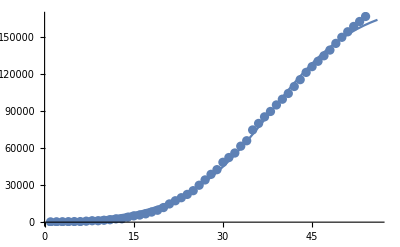

```mathematica
showplots[justdata,jdp0,justtime]
```

```mathematica
{jdp0,tp1,tp2,tp3}=GNiteration[justdata,jdp0,justtime]
```

{{181107.,1069.95,0.133754},9,2.21041×10^-7,54}

{213573.,3488.85,0.0989553}

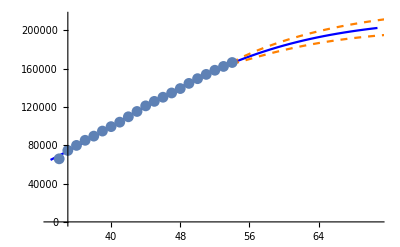
{-Graphics-,3566.74,977.115,4091,-12.588,77.9316}

```mathematica
{jp20,jabctab,jwinds}=stepGNiteration[justdata,jdp0,21,justtime,{1,0}];
jp20
jpdata20=justdata[[-21;;]];
datastats[jpdata20,jp20,1.8,2,justtime[[-21;;]]]
```

```mathematica
estimates[justdata,jdp0,28,justtime];
```

backward result : {83133.3,228.416,0.204937}

forward result : {196907.,2031.58,0.114478}

```mathematica
TableView[Transpose[generatestats[justdata,jdp0,28,justtime,jstartdate]]];
```

{981.19,4.49853,0.341492}

{1452.18,18.7219,0.227054}

{1452.18,18.7219,0.227054}

```mathematica
{"Russia",300,{133764.28972174952,345.7178233894532,0.17211220984196077},21,14,10,0}
```

```mathematica
{"Japan",950,{17986.663577976567,576.9474735585374,0.12382285884487645},21,14,8,0}
```

```mathematica
{name,trunc,cp0,lag,projt,bootl,drop}
```

```mathematica
{"Sweden",200,{23138.83457722449,461.922977379802,0.10293773671900139},28,14,10,0}
```

```mathematica
{"Spain",300,{215675.98160202175,3181.500137016704,0.14826151757050574},28,14,10,0}
```

```mathematica
{"Denmark",1100,{9249.181828199724,848.3550476707888,0.11809736637519559},28,14,10,0}
```

```mathematica
{"Greece",50,{2469.7252428688025,97.9216579531985,0.1381653045706424},21,14,10,0}
```

{Greece,50,{2469.73,97.9217,0.138165},21,14,10,0}

```mathematica
{"United Kingdom",200,{181106.79697173668,1069.9501757425367,0.1337539999625829},21,14,10,0}
```

backward result : {109233.,204.099,0.209633}

forward result : {213573.,3488.85,0.0989553}

last tab: {213573.,3488.85,0.0989553}

backward result : {109233.,204.099,0.209633}

forward result : {213573.,3488.85,0.0989553}

past errors : {{2627.17,3325.94,4485.05,6088.29,8767.16,11255.,13538.1,15901.4,18173.5,20732.7},10489.4}

boot tab : {{83241.9,195.501,0.211712},{78715.9,169.211,0.218966},{104119.,386.441,0.179579},{124173.,562.919,0.162089},{161690.,722.568,0.149431},{167872.,807.496,0.145055},{167177.,860.08,0.143001},{161292.,887.738,0.142526},{173543.,1053.12,0.13579},{164724.,1037.13,0.137269},{173159.,1212.29,0.131495},{191688.,1498.9,0.123273},{201406.,1708.79,0.1186},{216532.,2016.16,0.112684},{204744.,2024.87,0.113565},{199855.,2112.68,0.112913},{199191.,2256.34,0.111236},{206738.,2631.07,0.106331},{218142.,3158.27,0.100419},{233208.,3921.28,0.0935452},{245292.,4596.52,0.0886055},{256027.,5373.87,0.0839984},{266253.,6354.42,0.0792965},{271707.,7244.,0.0758797}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54}

April 30

-Graphics-

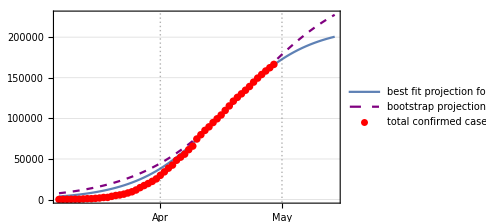

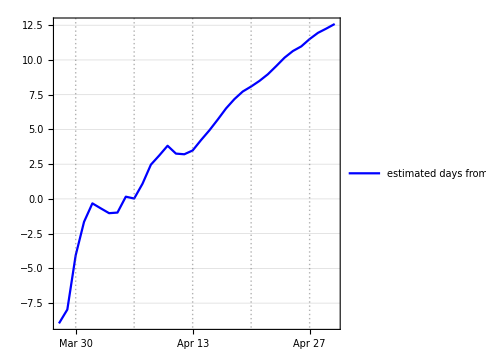

-Graphics-

```mathematica
{jgraf,jloggraf,jdfpplot,jprogplot,jfinal,cboo}=somegraphs[jdp0,jp20,justtime,justdata,jstartdate,21,14,0,10,1000];
jdatestring=reldatetostring[jstartdate,justtime[[-1]]]
jgraf
jloggraf
jdfpplot
jfinal
```